```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
GreedyAlgorithmFromCost[Cost_]:=((* 入力として枝のコストを与えられたときのGreedyアルゴリズムによる解法 *)
SortList=Ordering[Cost//N];(* 昇順 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
If[Length[VertexList[FindCycle[UndirectedGraph[AppendEdgeProcess]][[1]]]]==Length[Pin],EdgeSolution=AppendEdgeProcess]
]
]
];
EdgeSolution=FindCycle[UndirectedGraph[EdgeSolution]][[1]];
VertexSolution={1};
For[j=1,Length[VertexSolution]≠ Length[EdgeSolution],j++,
VertexSolution=Append[VertexSolution,EdgeSolution[[FirstPosition[EdgeSolution,VertexSolution[[j]]<->_][[1]],2]]]
];
VertexSolution=Append[VertexSolution,1]
)
```

### 渦電流の計算

```mathematica
Pin={{3.30204,9.09128},{3.30442,0.46863},{9.01646,6.24185},{9.31342,1.24199},{6.10577,2.96787},{5.75196,4.97666},{3.32525,5.95897},{1.84868,1.18248},{7.3017,7.41784},{4.80162,2.52861}}
(*Point input*)
```

{{3.30204,9.09128},{3.30442,0.46863},{9.01646,6.24185},{9.31342,1.24199},{6.10577,2.96787},{5.75196,4.97666},{3.32525,5.95897},{1.84868,1.18248},{7.3017,7.41784},{4.80162,2.52861}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

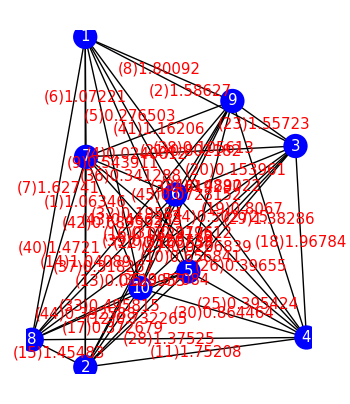

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### TSPの解

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

1→2 | 1→3 | 1→4 | 1→5 | 1→6 | 1→7 | 1→8 | 1→9 | 1→10 | 2→3
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

2→4 | 2→5 | 2→6 | 2→7 | 2→8 | 2→9 | 2→10 | 3→4 | 3→5 | 3→6
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

3→7 | 3→8 | 3→9 | 3→10 | 4→5 | 4→6 | 4→7 | 4→8 | 4→9 | 4→10
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

5→6 | 5→7 | 5→8 | 5→9 | 5→10 | 6→7 | 6→8 | 6→9 | 6→10 | 7→8
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

7→9 | 7→10 | 8→9 | 8→10 | 9→10
41 | 42 | 43 | 44 | 45

```mathematica
Curr
```

{1.06346,-1.58627,-0.619287,-0.0240012,-0.276503,1.07221,1.62741,-1.80092,0.543911,0.656841,1.75208,0.732265,0.0123955,-1.04089,-1.45483,0.0329175,0.372679,-1.96784,-0.8067,0.153961,0.802182,-0.165538,1.55723,-0.502725,-0.395424,0.39655,0.0206839,-1.37525,1.38286,-0.864464,0.279612,-0.19584,-0.495815,0.489022,-0.57084,0.341288,0.318267,-0.105613,0.0120739,1.4721,-1.16206,0.689593,-0.466253,0.392588,-0.0728152}

```mathematica
Reverse[Ordering[Abs[Curr]]](* 降順 *)
```

{18,8,11,7,2,23,40,15,29,28,41,6,1,14,30,19,21,12,42,10,3,35,9,24,33,34,43,26,25,44,17,36,37,31,5,32,22,20,38,45,16,4,27,13,39}

```mathematica
PDSort=Ordering[PD//N](* 昇順 *)
```

{35,15,31,23,17,36,39,38,6,44,20,25,42,12,32,41,8,19,34,33,30,5,40,18,13,26,37,14,45,24,21,11,2,29,9,4,28,27,16,7,10,43,1,22,3}

```mathematica
NewCost=Abs[PD/Curr ]
```

{8.10813,4.02544,15.9647,280.601,17.319,2.92144,4.94113,2.40745,12.3767,12.3644,3.45792,5.12678,413.827,5.27469,1.11445,243.544,6.83321,2.54526,5.43047,22.7401,7.10342,53.,1.33523,11.1735,9.21159,13.0137,368.541,5.42808,4.69696,5.42725,7.29478,20.8531,9.31058,9.42262,2.41073,7.6709,17.1035,27.3788,217.498,3.39617,3.64491,5.41562,17.766,8.26641,75.4149}

```mathematica
NewCostSort=Ordering[NewCost](* 昇順 *)
```

{15,23,8,35,18,6,40,11,41,2,29,7,12,14,42,30,28,19,17,21,31,36,1,44,25,33,34,24,10,9,26,3,37,5,43,32,20,38,22,45,39,16,4,27,13}

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

{31.515,{1,9,3,4,2,8,10,5,6,7,1}}

-Graphics-

{1,7,6,5,10,2,8,4,3,9,1}

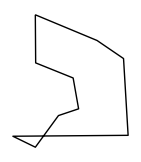

```mathematica
GreedyAlgorithmFromCost[PD]
Graphics[Line[Pin[[VertexSolution]]]]
```

```mathematica
GreedyAlgorithmFromCost[Abs[1/Curr]]
Graphics[Line[Pin[[VertexSolution]]]]
```

{1,9,3,4,2,5,6,10,7,8,1}

-Graphics-

{1,9,3,4,6,10,5,2,8,7,1}

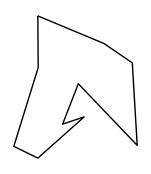

```mathematica
GreedyAlgorithmFromCost[Abs[PD/Curr]]
Graphics[Line[Pin[[VertexSolution]]]]
```

```mathematica
ArcLength[Line[Pin[[VertexSolution]]]]//N
```

34.0938

```mathematica
WeightFx[x_]:=x
```

```mathematica
WeightedData[PDSort,WeightFx]["Weights"]
```

{70,30,62,46,34,72,78,76,12,88,40,50,84,24,64,82,16,38,68,66,60,10,80,36,26,52,74,28,90,48,42,22,4,58,18,8,56,54,32,14,20,86,2,44,6}

```mathematica
WeightedData[…]
```

```mathematica
PDSort
```

{35,15,31,23,17,36,39,38,6,44,20,25,42,12,32,41,8,19,34,33,30,5,40,18,13,26,37,14,45,24,21,11,2,29,9,4,28,27,16,7,10,43,1,22,3}

{1,9,3,4,6,10,5,2,8,7,1}

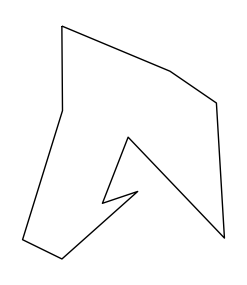

```mathematica
GreedyAlgorithmFromCost[Abs[PD/Curr]]
Graphics[Line[Pin[[VertexSolution]]]]
```

```mathematica
PD
```

{8.62265,6.38544,9.88676,6.73476,4.78876,3.1324,8.04123,4.33563,6.73182,8.12142,6.05856,3.75417,5.1296,5.49038,1.62135,8.01684,2.54659,5.00867,4.38076,3.50109,5.69824,8.7735,2.07927,5.61721,3.64248,5.1606,7.62287,7.46498,6.49524,4.69167,2.03971,4.08387,4.61632,4.60787,1.37614,2.61799,5.44347,2.89155,2.62604,4.99951,4.23562,3.73457,8.28343,3.24529,5.49135}

```mathematica
PD^2
```

{74.3501,40.7738,97.748,45.3571,22.9322,9.8119,64.6614,18.7977,45.3174,65.9575,36.7062,14.0938,26.3128,30.1443,2.62876,64.2698,6.48513,25.0868,19.1911,12.2577,32.4699,76.9743,4.32335,31.553,13.2677,26.6318,58.1081,55.7259,42.1881,22.0117,4.16042,16.678,21.3104,21.2325,1.89376,6.85385,29.6314,8.36105,6.89609,24.9951,17.9405,13.947,68.6151,10.5319,30.155}

```mathematica
FirstPosition[PDSort,2]
```

{33}

```mathematica
PD[[2]]FirstPosition[PDSort,2][[1]]
```

210.72

```mathematica
WeightPD=Table[PD[[i]]FirstPosition[PDSort,i][[1]],{i,Length[PD]}]
```

{370.774,210.72,444.904,242.452,105.353,28.1916,321.649,73.7057,235.614,332.978,193.874,52.5583,128.24,153.731,3.24269,312.657,12.733,120.208,78.8537,38.512,176.645,386.034,8.31707,168.516,43.7098,134.176,289.669,276.204,220.838,98.525,6.11913,61.258,92.3264,87.5496,1.37614,15.7079,146.974,23.1324,18.3823,114.989,67.7699,48.5495,347.904,32.4529,159.249}

{1,7,6,5,10,2,8,4,3,9,1}

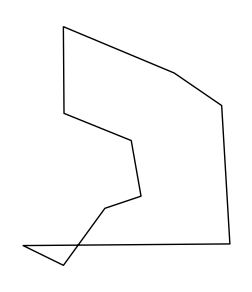

```mathematica
GreedyAlgorithmFromCost[Abs[WeightPD/Curr]]
Graphics[Line[Pin[[VertexSolution]]]]
```

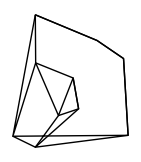

```mathematica
Show[-Graphics-,-Graphics-]
```

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

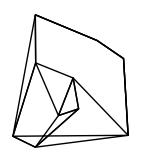

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```